Lengths(Fig17 theory) = {2082,2082}

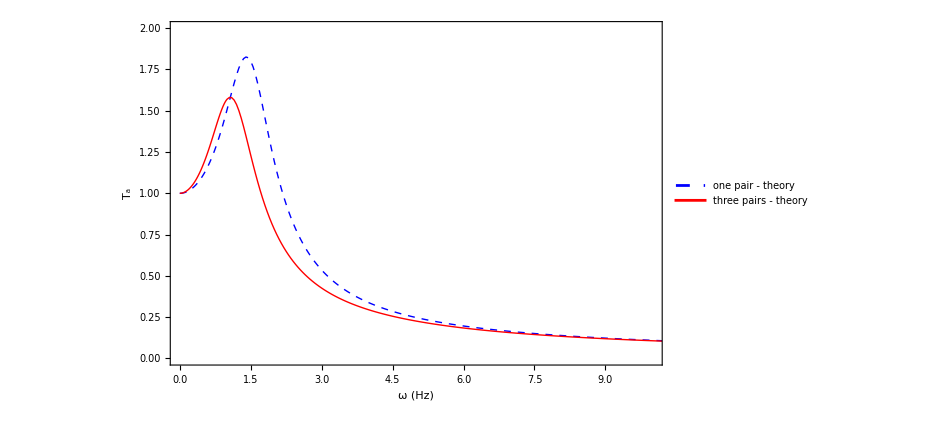

```mathematica
(* =====================Fig.17 ONLY (THEORY):0–100 Hz=====================*)ClearAll["Global`*"];
(*----------Core equations (Eq.(30)(28)(31))----------*)

(*Eq.(30):amplitude equation g(Z)=0*)
gEq30[Ω_?NumericQ,Z_?NumericQ,mu1_?NumericQ,mu3_?NumericQ,ζ_?NumericQ,Ze_?NumericQ]:=((3/4)*Ze^2*mu3*Z^3+(mu1-Ω^2)*Z)^2+(2*ζ*Ω*Z)^2-Ω^4;

(*Eq.(28):cos(phi)*)
cosPhi[Ω_?NumericQ,Z_?NumericQ,mu1_?NumericQ,mu3_?NumericQ,Ze_?NumericQ]:=(((3/4)*Ze^2*mu3*Z^3+(mu1-Ω^2)*Z)/Ω^2);

(*Eq.(31):transmissibility*)
TaVal[Z_?NumericQ,cphi_?NumericQ]:=Sqrt[1+2*Z*cphi+Z^2];

(*----------FindRoot continuation (for theory curve)----------*)
ZhatContinuation[Ωlist_List,mu1in_,mu3in_,ζin_,Zein_,Zinit_:10^-6]:=Module[{mu1,mu3,ζ,Ze,Zprev,sol,Znow,out={},Ω,wp=60},mu1=SetPrecision[mu1in,wp];
mu3=SetPrecision[mu3in,wp];
ζ=SetPrecision[ζin,wp];
Ze=SetPrecision[Zein,wp];
Zprev=SetPrecision[Zinit,wp];
Do[Ω=SetPrecision[ω,wp];
sol=Quiet@Check[FindRoot[gEq30[Ω,z,mu1,mu3,ζ,Ze]==0,{z,Zprev},WorkingPrecision->wp,AccuracyGoal->25,PrecisionGoal->25,MaxIterations->200],$Failed];
(*fallback*)If[sol===$Failed,sol=Quiet@Check[FindRoot[gEq30[Ω,z,mu1,mu3,ζ,Ze]==0,{z,Max[10^-10,0.5 Zprev+10^-8]},WorkingPrecision->wp,AccuracyGoal->25,PrecisionGoal->25,MaxIterations->200],$Failed];];
If[sol===$Failed,Continue[]];
Znow=z/. sol//N[#,30]&;
If[!NumericQ[Znow]||Znow<=0,Continue[]];
Zprev=Znow;
AppendTo[out,{N[Ω,20],N[Znow,20]}],{ω,Ωlist}];
out];

(* =====================Fig.17 parameters (from paper)=====================*)
ζ17=0.15;
Ze17=0.0353;
f0=3.5;                 (*resonance frequency (Hz)*)
ΩfromHz[f_]:=f/f0;

muOne17={0.1907,1.3836};
muThree17={0.1188,1.2344};

(* =====================Frequency list:0–100 Hz=====================*)
(*IMPORTANT:do NOT include exactly 0 Hz because cosPhi has 1/Ω^2.*)
fList17=Join[{0.001},Range[0.01,1.0,0.01],Range[1.0,100.0,0.05]];
Ωlist17=ΩfromHz/@N[fList17];

(* =====================Compute Z-hat via continuation=====================*)
ZhatOne=ZhatContinuation[Ωlist17,muOne17[[1]],muOne17[[2]],ζ17,Ze17,10^-6];
ZhatThree=ZhatContinuation[Ωlist17,muThree17[[1]],muThree17[[2]],ζ17,Ze17,10^-6];

(* =====================Convert to (Hz,Ta)=====================*)
data17OneTheory=Table[With[{Om=ZhatOne[[i,1]],Z=ZhatOne[[i,2]],c=cosPhi[ZhatOne[[i,1]],ZhatOne[[i,2]],muOne17[[1]],muOne17[[2]],Ze17]},{Om*f0,TaVal[Z,c]}],{i,Length[ZhatOne]}];

data17ThreeTheory=Table[With[{Om=ZhatThree[[i,1]],Z=ZhatThree[[i,2]],c=cosPhi[ZhatThree[[i,1]],ZhatThree[[i,2]],muThree17[[1]],muThree17[[2]],Ze17]},{Om*f0,TaVal[Z,c]}],{i,Length[ZhatThree]}];

Print["Lengths(Fig17 theory) = ",Length/@{data17OneTheory,data17ThreeTheory}];

(* =====================Plot (paper-like)=====================*)
baseStyle={FontFamily->"Times New Roman",FontSize->14};
frameCommon={Frame->True,Axes->False,FrameStyle->Black,BaseStyle->baseStyle,ImagePadding->{{55,20},{45,15}},PlotRangeClipping->True};
ticksMain={{Automatic,None},{Automatic,None}};
ticksInset={{Automatic,Automatic},{Automatic,Automatic}};

(*inset:use 60–100 Hz tail (more meaningful than 6–10 when range is 0–100)*)
fig17Inset=ListLinePlot[{data17OneTheory,data17ThreeTheory},Evaluate@frameCommon,FrameTicks->ticksInset,PlotRange->{{6,10},{0,0.25}},PlotStyle->{Directive[Blue,Dashed,Thick],Directive[Red,Thick]},ImageSize->260];

fig17Theory=Show[ListLinePlot[{data17OneTheory,data17ThreeTheory},Evaluate@frameCommon,FrameTicks->ticksMain,PlotRange->{{0,10},{0,2}},FrameLabel->{Style[Row[{TraditionalForm[ω]," (Hz)"}],18,Italic],Style[TraditionalForm[Subscript[T,a]],18,Italic]},PlotLegends->Placed[LineLegend[{"one pair - theory","three pairs - theory"},LabelStyle->baseStyle,LegendFunction->(Framed[#,FrameStyle->None,Background->None,FrameMargins->0]&)],{0.70,0.85}],PlotStyle->{Directive[Blue,Dashed,Thick],Directive[Red,Thick]},ImageSize->700],Epilog->{Inset[fig17Inset,Scaled[{0.70,0.55}]]}];

fig17Theory

(*Optional export*)
(*Export["Fig17_theory_0to100Hz.png",fig17Theory,ImageResolution->300];
Export["Fig17_onepair_theory_0to100Hz.csv",data17OneTheory];
Export["Fig17_threepairs_theory_0to100Hz.csv",data17ThreeTheory];*)
```